```mathematica
bm001=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_001","Table"];
bm003=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_003","Table"];
bm005=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_005","Table"];
bm007=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_007","Table"];
bm009=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_009","Table"];
bm0011=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_0011","Table"];
bm0013=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_0013","Table"];
bm0015=Import["Google Drive/jie_programs/QHlattice/test_error/test_error_normality_0015","Table"];
bm={bm001,bm003,bm005,bm007,bm009,bm0011};
n=Map[Length,bm];
x=Table[Table[j*0.5*4/n[[i]],{j,n[[i]]}],{i,6}];
nom=Table[Table[bm[[i]][[j]][[2]],{j,n[[i]]}],{i,6}];
normality=Table[Table[{x[[i]][[j]],bm[[i]][[j]][[2]]},{j,n[[i]]}],{i,6}];
avenormality=Table[{4*0.5/n[[i]],Total[nom[[i]]]/n[[i]]},{i,6}];
```

```mathematica
(*ListPlot[{ϕ1dif,ϕ2dif,ϕ3dif},PlotLegends->{"div[ϕ1]","div[ϕ2]", "div[ϕ3]"},PlotMarkers->Automatic, PlotLabel->"div[ϕ] - - - x (x: length of square loop)"]*)
```

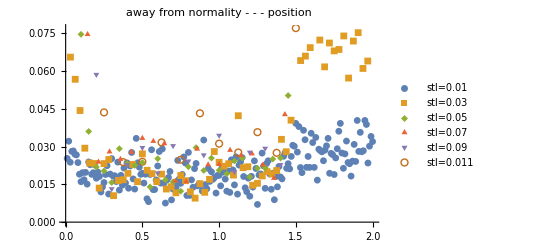

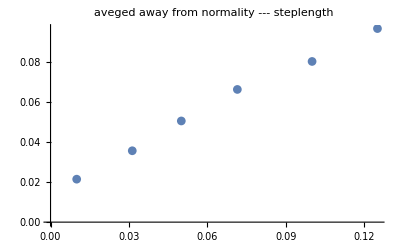

```mathematica
ListPlot[{normality[[1]],normality[[2]],normality[[3]],normality[[4]],normality[[5]],normality[[6]]},PlotLabel->"away from normality - - - position",PlotMarkers->{Automatic,7},PlotLegends->{"stl=0.01","stl=0.03","stl=0.05","stl=0.07","stl=0.09","stl=0.011","stl=0.013","stl=0.015"}]

ListPlot[avenormality,PlotMarkers->Automatic, PlotLabel->"aveged away from normality --- steplength"]
```